Approximation of PRDM9 diversity (Ke) as a function of ε

## Using linear system

```mathematica
x = x1 *eps + x2 * eps ^2
```

eps x1+eps^2 x2

```mathematica
y = y1 *eps + y2 * eps ^2
```

eps y1+eps^2 y2

```mathematica
Series[y* x , {eps,0, 3}]
```

x1 y1 eps^2+(x2 y1+x1 y2) eps^3+O[eps]^4

```mathematica
Series[eps^2(1-y)^2   , {eps,0, 3}]
```

eps^2-2 y1 eps^3+O[eps]^4

```mathematica
Series[eps^2(1-y)^2 -y* x  , {eps,0, 3}]
```

(1-x1 y1) eps^2+(-2 y1-x2 y1-x1 y2) eps^3+O[eps]^4

```mathematica
Series[(1-y)(1+ x/2 + x^2/3) , {eps,0, 2}]
```

1+(x1/2-y1) eps+1/6 (2 x1^2+3 x2-3 x1 y1-6 y2) eps^2+O[eps]^3

```mathematica
Solve[(x1/2-y1)==0&&1/6 (2 x1^2+3 x2-3 x1 y1-6 y2)==0&&x1 y1 ==1 &&(x2 y1+x1 y2)==-2 y1,{x1,y1, x2, y2}]
```

{{x1→-√2,y1→-1/(√2),x2→-7/6,y2→-5/12},{x1→√2,y1→1/(√2),x2→-7/6,y2→-5/12}}

## Second order approximation

```mathematica
ClearAll["Global`*"]
```

### Second order approximation of Mimimun activity (Linf) as a function of L

```mathematica
SX= x/.Solve[L(x+x^2/2)==x, x]
```

{0,-(2 (-1+L))/L}

```mathematica
Linf= FullSimplify[1+SX[[2]]]
```

-1+2/L

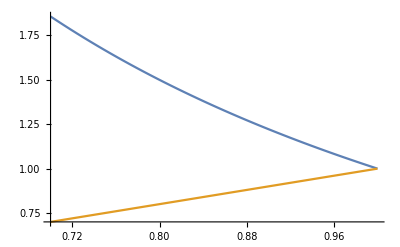

```mathematica
Plot[{Linf,L},{L,0.7,1}]
```

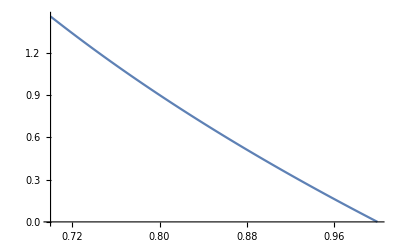

```mathematica
Plot[1- 2 *L +Linf,{L,0.7,1}]
```

### Solving Mean activity (L) as a function of ε

```mathematica
SL=L /. Solve[(1-L) (1-Linf)/ (L^2) == eps,L]
```

{-2/(3 eps)+(-4-12 eps)/(3 eps (8+36 eps+27 eps^2+3 √3 √(8 eps^3+27 eps^4))^(1/3))-((8+36 eps+27 eps^2+3 √3 √(8 eps^3+27 eps^4))^(1/3))/(3 eps),-2/(3 eps)-((1+ⅈ √3) (-4-12 eps))/(6 eps (8+36 eps+27 eps^2+3 √3 √(8 eps^3+27 eps^4))^(1/3))+((1-ⅈ √3) (8+36 eps+27 eps^2+3 √3 √(8 eps^3+27 eps^4))^(1/3))/(6 eps),-2/(3 eps)-((1-ⅈ √3) (-4-12 eps))/(6 eps (8+36 eps+27 eps^2+3 √3 √(8 eps^3+27 eps^4))^(1/3))+((1+ⅈ √3) (8+36 eps+27 eps^2+3 √3 √(8 eps^3+27 eps^4))^(1/3))/(6 eps)}

```mathematica
L= First[SL]
```

-2/(3 eps)+(-4-12 eps)/(3 eps (8+36 eps+27 eps^2+3 √3 √(8 eps^3+27 eps^4))^(1/3))-((8+36 eps+27 eps^2+3 √3 √(8 eps^3+27 eps^4))^(1/3))/(3 eps)

### PRDM9 diversity (Ke) as a function of ε

#### rho = Ne * v * r_0 / \alpha

```mathematica
K= FullSimplify[ 4 rho * L /(1- 2 *L +Linf)]
```

(2 (2+(4+12 eps)/((8+9 eps (4+3 eps)+3 √3 √(eps^3 (8+27 eps)))^(1/3))+(8+9 eps (4+3 eps)+3 √3 √(eps^3 (8+27 eps)))^(1/3))^2 rho)/(9 eps^2 (1-1/(9 eps^2)(2+(4+12 eps)/((8+9 eps (4+3 eps)+3 √3 √(eps^3 (8+27 eps)))^(1/3))+(8+9 eps (4+3 eps)+3 √3 √(eps^3 (8+27 eps)))^(1/3))^2))

### First order approximation of Ke

```mathematica
FullSimplify[Series[K,{eps,0,1}]]
```

-2 rho+O[eps]^(3/2)

## Third order approximation

```mathematica
ClearAll["Global`*"]
```

### Third order approximation of Mimimun activity (Linf) as a function of L

```mathematica
SX = x /.Solve[L(1+x/2+x^2/3)==1, x]
```

{(3 (-L-(√(16 L-13 L^2))/(√3)))/(4 L),(3 (-L+(√(16 L-13 L^2))/(√3)))/(4 L)}

```mathematica
Linf= FullSimplify[1-SX[[2]]]
```

7/4-(√(48-39 L))/(4 √L)

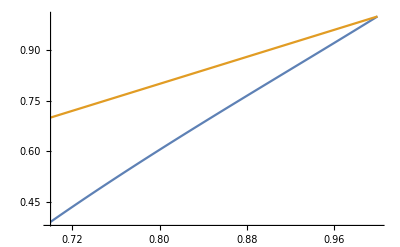

```mathematica
Plot[{Linf,L},{L,0.7,1}]
```

```mathematica
FullSimplify[1- 2 *L +Linf]
```

1/4 (5+(√(48-39 L))/(√L)-8 L)

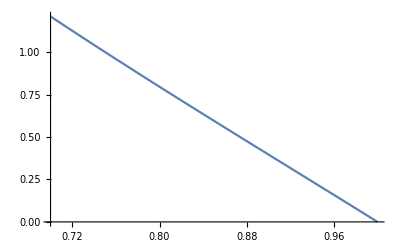

```mathematica
Plot[1- 2 *L +Linf,{L,0.7,1}]
```

### Solving mean activity (L) as a function of ε (v ro / u \alpha )

```mathematica
Solve[(1-L) (1-Linf)/ (L^2) == eps,L]
```

{{L→Root[-6+18 #1-18 #1^2+(6-3 eps) #1^3+3 eps #1^4+2 eps^2 #1^5&,1]},{L→Root[-6+18 #1-18 #1^2+(6-3 eps) #1^3+3 eps #1^4+2 eps^2 #1^5&,2]},{L→Root[-6+18 #1-18 #1^2+(6-3 eps) #1^3+3 eps #1^4+2 eps^2 #1^5&,3]},{L→Root[-6+18 #1-18 #1^2+(6-3 eps) #1^3+3 eps #1^4+2 eps^2 #1^5&,4]},{L→Root[-6+18 #1-18 #1^2+(6-3 eps) #1^3+3 eps #1^4+2 eps^2 #1^5&,5]}}

### Approximation of mean activity (L) as a function of ε

```mathematica
serie= Series[(1-L) (1-Linf)/ (L^2),{L,1,3}]
```

2 (L-1)^2-10/3 (L-1)^3+O[L-1]^4

```mathematica
SL = L/. Solve[Normal[serie ]== eps,L]
```

{1/5 (6-2^(2/3)/((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))-((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))/2^(2/3)),6/5+(1+ⅈ √3)/(5 2^(1/3) (-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))+((1-ⅈ √3) (-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))/(10 2^(2/3)),6/5+(1-ⅈ √3)/(5 2^(1/3) (-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))+((1+ⅈ √3) (-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))/(10 2^(2/3))}

```mathematica
L= SL[[1]]
```

1/5 (6-2^(2/3)/((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))-((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))/2^(2/3))

```mathematica
FullSimplify[Series[L,{eps,0,2}]]
```

1-(√eps)/(√2)+(5 eps)/12-(125 eps^(3/2))/(144 √2)+(125 eps^2)/108+O[eps]^(5/2)

```mathematica
FullSimplify[Series[Linf,{eps,0,2}]]
```

1-√2 √eps+(7 eps)/6-(301 eps^(3/2))/(72 √2)+(403 eps^2)/54+O[eps]^(5/2)

### PRDM9 diversity (Ke) as a function of ε

#### rho = Ne * v * r_ 0 / \alpha

```mathematica
K = 4rho * L /(1- 2 *L +Linf)
```

(4 (6+2^(2/3)/((4+75 eps+5 √3 √(8 eps+75 eps^2))^(1/3))+((4+75 eps+5 √3 √(8 eps+75 eps^2))^(1/3))/2^(2/3)) rho)/(5 (1-2/5 (6+2^(2/3)/((4+75 eps+5 √3 √(8 eps+75 eps^2))^(1/3))+((4+75 eps+5 √3 √(8 eps+75 eps^2))^(1/3))/2^(2/3))+(5 (1/5 (6+2^(2/3)/((4+75 eps+5 √3 √(8 eps+75 eps^2))^(1/3))+((4+75 eps+5 √3 √(8 eps+75 eps^2))^(1/3))/2^(2/3))+(√(6+2^(2/3)/((4+75 eps+5 √3 √(8 eps+75 eps^2))^(1/3))+((4+75 eps+5 √3 √(8 eps+75 eps^2))^(1/3))/2^(2/3)) √(48-39/5 (6+2^(2/3)/((4+75 eps+5 √3 √(8 eps+75 eps^2))^(1/3))+((4+75 eps+5 √3 √(8 eps+75 eps^2))^(1/3))/2^(2/3))))/(√5)))/(4 (6+2^(2/3)/((4+75 eps+5 √3 √(8 eps+75 eps^2))^(1/3))+((4+75 eps+5 √3 √(8 eps+75 eps^2))^(1/3))/2^(2/3)))))

```mathematica
FullSimplify[Series[K,{eps,0,2}]]
```

(-832/291-(320 ⅈ)/291) rho+(245000/254043+(90500 ⅈ)/254043) rho eps+(-405828125/98568684-(120996875 ⅈ)/197137368) rho eps^2+O[eps]^(5/2)